This notebook generates band structure of Projected Weyl SemiMetal (PWSM) in a magnetic field

Here we take k_z to be a good quantum number

```mathematica
tStart=AbsoluteTime[];
```

```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
(**Change the system size here **)
```

```mathematica
Lx=32;
Ly=32;
A=Lx*Ly;
```

```mathematica
B=1/Ly;
```

```mathematica
(*--- We choose gauge A = (-By,0,0) ---*)
```

```mathematica
(**-----------------Define the sine and cosine matrices for the parent square lattice--------------------**)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2 Exp[I B k],sx2d[j+1+k Lx,j+k Lx]=I/2 Exp[-I B k]},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2 Exp[I B k],sx2dp[1+k Lx,(k+1)Lx]=I/2 Exp[-I B k]},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2 Exp[I B k],cx2d[j+1+k Lx,j+k Lx]=1/2 Exp[-I B k]},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2 Exp[I B k],cx2dp[1+k Lx,(1+k)Lx]=1/2 Exp[-I B k]},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix for the parent square lattice---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM1]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
(** Define Hamiltonian **)
(** We will use mixed boundary conditions, PBC in x and OBC in y.Therefore, αx = 1 and αy = 0 **)
```

```mathematica
HamiltonianWSM1[t_,t0_,m_,tz_,kz_,αx_, αy_]:=t*(KroneckerProduct[SX2D+αx*SX2DP,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+KroneckerProduct[2*Cons-2t0*(CX2D+CY2D+αx*CX2DP+αy*CY2DP),σ3]+KroneckerProduct[(tz *Cos[kz]-m)*Cons,σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(** Generate a vector where values of kz for which we will diagonalize the Hamiltonian is stored **)
```

```mathematica
Clear[kzVector]
```

```mathematica
kzVector = N@Subdivide[-π+0.0001,π-0.0001,50]
```

{-3.14149,-3.01583,-2.89017,-2.76451,-2.63885,-2.51319,-2.38753,-2.26187,-2.13622,-2.01056,-1.8849,-1.75924,-1.63358,-1.50792,-1.38226,-1.2566,-1.13094,-1.00528,-0.879618,-0.753958,-0.628299,-0.502639,-0.376979,-0.251319,-0.12566,0.,0.12566,0.251319,0.376979,0.502639,0.628299,0.753958,0.879618,1.00528,1.13094,1.2566,1.38226,1.50792,1.63358,1.75924,1.8849,2.01056,2.13622,2.26187,2.38753,2.51319,2.63885,2.76451,2.89017,3.01583,3.14149}

```mathematica
NumPoints=Dimensions[kzVector][[1]]
```

51

```mathematica
(*--------------------Projected Brane--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

2048

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
(** Comment/Uncomment the rational and irrational equations accordingly **)
```

```mathematica
(**-------Irrational-------**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+8
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+6
```

```mathematica
(**-------Rational-------**)
```

```mathematica
(** LineUp[x_]:=(2/3)(x-1)+8
LineDn[x_]:=(2/3)*(x-2)+6 **)
```

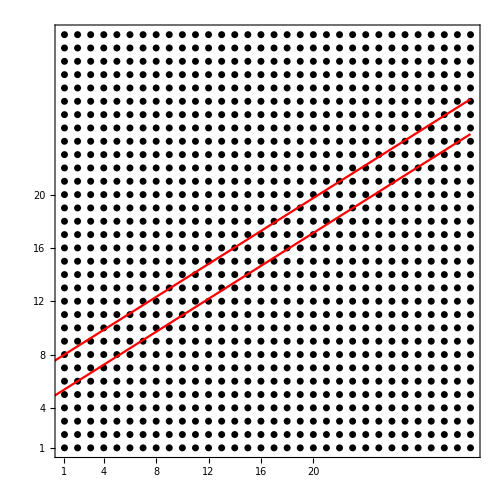

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron]
```

```mathematica
(**-----We want to isolate points inside the projected brane (between the red lines), store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew]
```

{161,193,194,195,226,227,228,229,259,260,261,262,293,294,295,296,326,327,328,329,330,360,361,362,363,394,395,396,397,427,428,429,430,461,462,463,464,494,495,496,497,498,528,529,530,531,562,563,564,565,595,596,597,598,599,629,630,631,632,663,664,665,666,696,697,698,699,730,731,732,733,763,764,765,766,767,797,798,799,800,831,832,864}

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
(**-- Fibondown=Table[Fibonlist[[j]]+A,{j,1,Dimensions[Fibonlist][[1]]}]; --**)
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon]
```

{321,322,385,386,387,388,389,390,451,452,453,454,455,456,457,458,517,518,519,520,521,522,523,524,585,586,587,588,589,590,591,592,651,652,653,654,655,656,657,658,659,660,719,720,721,722,723,724,725,726,787,788,789,790,791,792,793,794,853,854,855,856,857,858,859,860,921,922,923,924,925,926,927,928,987,988,989,990,991,992,993,994,995,996,1055,1056,1057,1058,1059,1060,1061,1062,1123,1124,1125,1126,1127,1128,1129,1130,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1257,1258,1259,1260,1261,1262,1263,1264,1325,1326,1327,1328,1329,1330,1331,1332,1391,1392,1393,1394,1395,1396,1397,1398,1459,1460,1461,1462,1463,1464,1465,1466,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1593,1594,1595,1596,1597,1598,1599,1600,1661,1662,1663,1664,1727,1728}

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

166

```mathematica
NOrbitalsQuasi/2
```

83

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

1882

```mathematica
PercentageDataIn = N[NOrbitalsQuasi/(2*A)]
```

0.0810547

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{2048}

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(**-------------------------------**)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*----------------------------Create matrices for the Hamiltonian of the projected brane, for different values of kz, using a loop-------------------------------------------*)
```

```mathematica
Clear[TabRenorEnergies]
```

```mathematica
TabRenorEnergies={}
```

{}

```mathematica
Do[{Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D],
HTrial = HamiltonianWSM1[1,0.5,4,1,kzVector[[p]],1,0],
(*---------------This is H11-----------------*)
Hfbfb[i_Integer,j_Integer]=0,
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
],
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}],
(*--------------------This is H22-----------------*)
H2d2d[i_Integer,j_Integer]=0,
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
],
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}],
(*------------------This is H21------------------*)
H2dfb[i_Integer,j_Integer]=0,

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
],
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}],
(*------------------This is H21------------------*)
Hfb2d[i_Integer,j_Integer]=0,

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
],
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}],

(*---------------------------------------------------------------------------------------------------------------------------------*)
Clear[HFibonRenor],
(** Sometimes the inverse does not exist because of a single zero eigenvalue -- we will regularize it **)
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D- 0.000001 IdentityMatrix[NOrbitalsOutside]].H2DFB),
(** This is the effective Hamiltonian HPTB, defined in Eq. 1 in our paper **)

OnlyEigenvalue=Eigenvalues[HFibonRenor],
NSitesInside = NOrbitalsQuasi/2,
Do[TabRenorEnergies = Append[TabRenorEnergies,{kzVector[[p]],OnlyEigenvalue[[i]]}],{i,1,NOrbitalsQuasi}]
},{p,2,NumPoints-1}]
```

```mathematica
TabRenorEnergies=Sort[Re[TabRenorEnergies]];
```

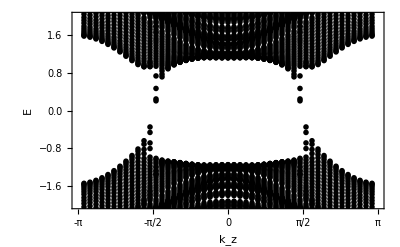

```mathematica
AA=Show[ListPlot[TabRenorEnergies,PlotRange-> { {-π,π } ,{-2,2}},PlotStyle->{PointSize[0.01],Black}],FrameTicks-> {{-π,-π/2,0,{π/2,"π/2"},π},Automatic,{},{}},BaseStyle-> 18,FrameLabel-> {"k_z","E"},Frame-> True,RotateLabel-> False,FrameStyle->{{Thick, Black},{Thick, Black},{Thick, Black},{Thick, Black}},Axes->{True, False}]
```

```mathematica
percentageOfOrbitalsInside = N[NOrbitalsQuasi/(2*A)]
```

0.0810547

```mathematica
(** Export["dataWSMZoomed+8and+6Irrationalm=4Parent32x32.dat",Re[TabRenorEnergies]]; **)
```

```mathematica
Dimensions[TabRenorEnergies]
```

{8134,2}

```mathematica
Dimensions[kzVector][[1]]*NOrbitalsQuasi
```

8466

```mathematica
{LandauLevelEnergies = {},Do[LandauLevelEnergies = Append[LandauLevelEnergies, TabRenorEnergies[[NOrbitalsQuasi/2+k*NOrbitalsQuasi]]],{k,0,Dimensions[kzVector][[1]]-3}]};
```

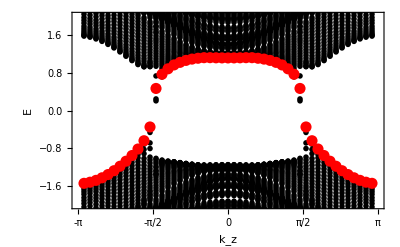

```mathematica
Show[AA,ListPlot[Re[LandauLevelEnergies],PlotStyle->{Red,PointSize[0.02]},PlotRange->{{-π/2,π/2},All}],
FrameStyle-> {Black,Black,Black,Black}]
```

```mathematica
(*---------Export the data in the plot above -------*)
```

```mathematica
(** Export["dataLandauLevels+8and+6Irrationalm=4Parent32x32.dat",TabRenorEnergies]; **)
```

```mathematica
tStop=AbsoluteTime[];
timeTakenInSeconds = tStop - tStart
```

1839.87052